## Data Handling

System & Directory

```mathematica
os = "linux";
baselinux = "~/repos/fp/AFM";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.txt"];
```

Files listing

```mathematica
(*  For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames⟦i⟧]]; *)
```

Data generation

```mathematica
data[num_] := Drop[Import[fnames⟦num⟧, "Table"], 4]
```

## Analysis

Plot the different Images 
‘res’ specifies the resolution, set to ‘1’ for full resolution
‘offset’ is 1
i --> image number - offset
j --> real map or derrivative
k --> determines scanning direction

```mathematica
res = 30; offset = 1;
Manipulate[{ListPlot3D[
					data[offset+4i+2k+j]⟦;; ;;res⟧,
					ColorFunction->"AvocadoColors",InterpolationOrder->1,ImageSize->800,Mesh->None
					],
		 fnames[[offset+4i+2k+j]]
		},
		{{i,0,Image Number},Range[0,(Length[fnames]-offset)/4]} ,
		{{j,1,"Type"},{1.0->"Height",0->"Derrivative"}},
		{{k,0,"Scanning Direction"},{0->"Forward",1.0->"Backward"}}
						];
```

```mathematica
Zeilenlaenge=256; Datansatz=50;
datamatrix=Table[data[Datansatz]⟦1+i*Zeilenlaenge;;Zeilenlaenge*(i+1)⟧,{i,0,Zeilenlaenge-1}]
```

$Aborted

```mathematica
Ad=0;Au=0;
For[i=1, i<Zeilenlaenge,
	For[k=1, k<Zeilenlaenge,
Ad+=Norm[(datamatrix⟦k⟧⟦i+1⟧-datamatrix⟦k⟧⟦i⟧)×(datamatrix⟦k+1⟧⟦i⟧-datamatrix⟦k⟧⟦i⟧)]/2;
Au+=Norm[(datamatrix⟦k⟧⟦i+1⟧-datamatrix⟦k+1⟧⟦i+1⟧)×(datamatrix⟦k+1⟧⟦i⟧-datamatrix⟦k+1⟧⟦i+1⟧)]/2
;k+=1];
i+=1];
A=Ad+Au
```

2493.12

```mathematica
NumberForm[A,30]
```

2493.116771966427

### Roughness

```mathematica
dmatrix[dat_,rowlength_]:=Partition[data[dat],rowlength]
```

```mathematica
surface[dat_]:=(Ad=0;Au=0;
For[i=1, i<Zeilenlaenge,
	For[k=1, k<Zeilenlaenge,
Ad+=Norm[(dat⟦k⟧⟦i+1⟧-dat⟦k⟧⟦i⟧)×(dat⟦k+1⟧⟦i⟧-dat⟦k⟧⟦i⟧)]/2;
Au+=Norm[(dat⟦k⟧⟦i+1⟧-dat⟦k+1⟧⟦i+1⟧)×(dat⟦k+1⟧⟦i⟧-dat⟦k+1⟧⟦i+1⟧)]/2
;k+=1];
i+=1];Return[Ad+Au])
```

```mathematica
rough[dat_,rowlength_:2^8]:=ScientificForm[surface[dmatrix[dat,rowlength]]/(Last[data[dat]]⟦1⟧*Last[data[dat]]⟦2⟧)-1]
```

TESTSECTION

```mathematica
rlist=Map[rough,{2,4,6,8}];
```

```mathematica
dat=data[50];
```

```mathematica
ifun=Interpolation[data[50]]
```

```mathematica
ifun[3,5]
```

0.0173011

```mathematica
Plot3D[ifun[x,y],{x,0,50},{y,0,50}]
```

-Graphics3D-

```mathematica
inlist=ListInterpolation[dat]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3, 2}.

InterpolatingFunction[{{1.,65536.},{1.,3.}},<>]

```mathematica
if1[3,5]
```

InterpolatingFunction[{{0.,0.,0.024881},{0.195555,0.,0.0245933},{0.391111,0.,0.0246162},{0.586666,0.,0.0243285},{0.782221,0.,0.0243514},{0.977776,0.,0.0240637},{1.17333,0.,0.0240867},{1.36889,0.,0.0241096},{1.56444,0.,0.0241326},{1.76,0.,0.0238448},{1.95555,0.,0.0238678},«65514»,{47.911,49.995,0.00623309},{48.1066,49.995,0.00625603},{48.3022,49.995,0.00627898},{48.4977,49.995,0.00599125},{48.6933,49.995,0.00570353},{48.8888,49.995,0.00541581},{49.0844,49.995,0.00512808},{49.2799,49.995,0.00515103},{49.4755,49.995,0.0048633},{49.671,49.995,0.00457558},{49.8666,49.995,0.00459852}}][3,5]

```mathematica
ipoly=InterpolatingPolynomial[idat,{x,y,z}]
```

InterpolatingPolynomial::ipab: Abscissa specification {0., 0.} in {{0., 0.}, 0.024881} is not a point in 3 dimensions.

InterpolatingPolynomial[{{{0.,0.},0.024881},{{0.195555,0.},0.0245933},{{0.391111,0.},0.0246162},{{0.586666,0.},0.0243285},{{0.782221,0.},0.0243514},{{0.977776,0.},0.0240637},{{1.17333,0.},0.0240867},{{1.36889,0.},0.0241096},{{1.56444,0.},0.0241326},{{1.76,0.},0.0238448},{{1.95555,0.},0.0238678},«65514»,{{47.911,49.995},0.00623309},{{48.1066,49.995},0.00625603},{{48.3022,49.995},0.00627898},{{48.4977,49.995},0.00599125},{{48.6933,49.995},0.00570353},{{48.8888,49.995},0.00541581},{{49.0844,49.995},0.00512808},{{49.2799,49.995},0.00515103},{{49.4755,49.995},0.0048633},{{49.671,49.995},0.00457558},{{49.8666,49.995},0.00459852}},{x,y,z}]

```mathematica
Plot3D[ipoly,{x,1,40},{y,1,40}]
```

InterpolatingPolynomial::ipab: Abscissa specification 0. in {0., 0., 0.024881} is not a point in 3 dimensions.

General::stop: Further output of InterpolatingPolynomial :: ipab will be suppressed during this calculation.

-Graphics3D-

```mathematica
dat
```

{{0.,0.,0.024881},{0.195555,0.,0.0245933},{0.391111,0.,0.0246162},{0.586666,0.,0.0243285},{0.782221,0.,0.0243514},{0.977776,0.,0.0240637},{1.17333,0.,0.0240867},{1.36889,0.,0.0241096},{1.56444,0.,0.0241326},{1.76,0.,0.0238448},{1.95555,0.,0.0238678},{2.15111,0.,0.0238907},«65512»,{47.7155,49.995,0.00621014},{47.911,49.995,0.00623309},{48.1066,49.995,0.00625603},{48.3022,49.995,0.00627898},{48.4977,49.995,0.00599125},{48.6933,49.995,0.00570353},{48.8888,49.995,0.00541581},{49.0844,49.995,0.00512808},{49.2799,49.995,0.00515103},{49.4755,49.995,0.0048633},{49.671,49.995,0.00457558},{49.8666,49.995,0.00459852}}

```mathematica
Dimensions[dat]
```

{65536,3}

```mathematica
Last[dat]
```

{49.8666,49.995,0.00459852}

```mathematica
idat=Table[{{dat⟦i⟧⟦1⟧,dat⟦i⟧⟦2⟧},dat⟦i⟧⟦3⟧},{i,1,65536}]
```

{{{0.,0.},0.024881},{{0.195555,0.},0.0245933},{{0.391111,0.},0.0246162},{{0.586666,0.},0.0243285},{{0.782221,0.},0.0243514},{{0.977776,0.},0.0240637},{{1.17333,0.},0.0240867},{{1.36889,0.},0.0241096},«65521»,{{48.6933,49.995},0.00570353},{{48.8888,49.995},0.00541581},{{49.0844,49.995},0.00512808},{{49.2799,49.995},0.00515103},{{49.4755,49.995},0.0048633},{{49.671,49.995},0.00457558},{{49.8666,49.995},0.00459852}}

```mathematica
ipoly=InterpolatingPolynomial[idat,{x,y}]
```

InterpolatingPolynomial::list: List expected at position 1 in InterpolatingPolynomial[idat, {x, y}].

InterpolatingPolynomial[idat,{x,y}]

```mathematica
idat[[1;;10]]
```

{{{0.,0.},0.024881},{{0.195555,0.},0.0245933},{{0.391111,0.},0.0246162},{{0.586666,0.},0.0243285},{{0.782221,0.},0.0243514},{{0.977776,0.},0.0240637},{{1.17333,0.},0.0240867},{{1.36889,0.},0.0241096},{{1.56444,0.},0.0241326},{{1.76,0.},0.0238448}}

```mathematica
parfit=Fit[dat,{1,x^2,y^2,x^3,y^3},{x,y}]
```

0.0207084-0.0000104577 x^2+2.35427×10^-7 x^3+5.33799×10^-6 y^2-1.17235×10^-7 y^3

```mathematica
Plot3D[parfit,{x,0,50},{y,0,50}]
```

-Graphics3D-

```mathematica
ListPlot3D[parfit[2,3]]
```

ListPlot3D::arrayerr: (0.0207084  - 0.0000104577\ x^2 + 2.35427×10^-7\ x^3 + 5.33799×10^-6\ y^2 - 1.17235×10^-7\ y^3)[2, 3] must be a valid array or a list of valid arrays.

ListPlot3D[(0.0207084-0.0000104577 x^2+2.35427×10^-7 x^3+5.33799×10^-6 y^2-1.17235×10^-7 y^3)[2,3]]

```mathematica
dat-parfit
```

{{-0.0207084+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3,-0.0207084+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3,0.00417259+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3},{0.174847+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3,-0.0207084+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3,0.00388489+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3},«65533»,{49.8459+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3,49.9743+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3,-0.0161099+0.0000104577 x^2-2.35427×10^-7 x^3-5.33799×10^-6 y^2+1.17235×10^-7 y^3}}

(0.0206206+5.33799×10^-6 y^2-1.17235×10^-7 y^3)[3,y]

```mathematica
Map[parfit/.x,y,{{3,5},{2,1}}]
```

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Map::level: Level specification {{3, 5}, {2, 1}} is not of the form n, {n}, or {m, n}.

Map[0.0207084-0.0000104577 x^2+2.35427×10^-7 x^3+5.33799×10^-6 y^2-1.17235×10^-7 y^3/.x,y,{{3,5},{2,1}}]

```mathematica
cft=NonlinearModelFit[dat]
```

```mathematica
nlm=NonlinearModelFit[dat,a0+a1 x+ b1 y+a2 x^2+b2 y^2+a3 x^3+b3 y^3+a4 x^4+b4 y^4,{a0,a1,a2,a3,b1,b2,b3,a4,b4},{x,y}]
```

FittedModel[0.0252466-0.000324241 x-8.28593×10^-6 x^2+6.74452×10^-7 x^3-«22» «1»-«22» y+0.0000499668 y^2-1.27556×10^-6 y^3+1.00421×10^-8 y^4]

```mathematica
Normal[nlm]
```

0.0250424-0.000598239 x+0.0000165529 x^2-1.01386×10^-7 x^3-0.000275324 y+0.000017737 y^2-2.7145×10^-7 y^3

```mathematica
Show[ListPlot3D[dat],Plot3D[nlm[x,y],{x,0,50},{y,0,50}]]
```

-Graphics3D-

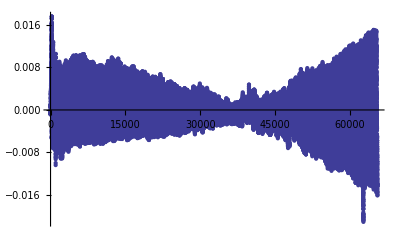

```mathematica
ListPlot[nlm["FitResiduals"]]
```

```mathematica
rdat=dmat
```

```mathematica
ListPlot3D[dmatrix[50,2^8]⟦1⟧]
```

-Graphics3D-

```mathematica
Dimensions[dmatrix[50,2^8]⟦1⟧⟦;;⟧⟦2⟧]
```

{3}

```mathematica
Dimensions[Transpose[ds2]]
```

{256,2}

```mathematica
ds2=Transpose[{dmatrix[50,2^8]⟦1⟧⟦All,1⟧,dmatrix[50,2^8]⟦1⟧⟦All,3⟧}];
```

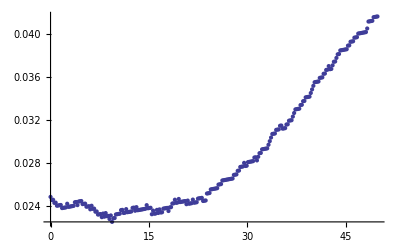

```mathematica
ListPlot[ds2]
```

```mathematica
dmatrix[dat_,rowlength_]:=Partition[data[dat],rowlength]
```

```mathematica
listdata[dat_,rowlength_:2^8]:=Table[ Transpose[{dmatrix[dat,2^8]⟦i⟧⟦All,1⟧,dmatrix[dat,2^8]⟦i⟧⟦All,3⟧}],{i,1,rowlength}]
```

```mathematica
ld50=listdata[50];
```

$Aborted

```mathematica
Partition[dat,50]
```

{{{0.,0.,0.024881},{0.195555,0.,0.0245933},{0.391111,0.,0.0246162},{0.586666,0.,0.0243285},{0.782221,0.,0.0243514},{0.977776,0.,0.0240637},{1.17333,0.,0.0240867},{1.36889,0.,0.0241096},{1.56444,0.,0.0241326},{1.76,0.,0.0238448},{1.95555,0.,0.0238678},{2.15111,0.,0.0238907},{2.34666,0.,0.0239137},«24»,{7.23555,0.,0.0232446},{7.4311,0.,0.0232675},{7.62666,0.,0.0232905},{7.82221,0.,0.0230028},{8.01777,0.,0.0233364},{8.21332,0.,0.0230487},{8.40888,0.,0.0233823},{8.60443,0.,0.0230945},{8.79999,0.,0.0231175},{8.99554,0.,0.0228298},{9.1911,0.,0.0231634},{9.38665,0.,0.022565},{9.58221,0.,0.0228986}},«1308»,{«1»}}

```mathematica
row=5
```

5

```mathematica
nllm=NonlinearModelFit[Take[dat,{(row-1)*256+1,row*256}]⟦All,{1,3}⟧,{a+b x+c x^2},{a,b,c},x]
```

FittedModel[0.016639-0.000256371 x+0.0000120145 x^2]

```mathematica
Normal[nllm[2]]
```

0.0198085

```mathematica
ListPlot[Take[dat,{1,256}]⟦All,{1,3}⟧]
```

-Graphics-

```mathematica
Manipulate[ListPlot[Take[dat,{(row-1)*256+1,row*256}]⟦All,{1,3}⟧],{row,1,256}]
```

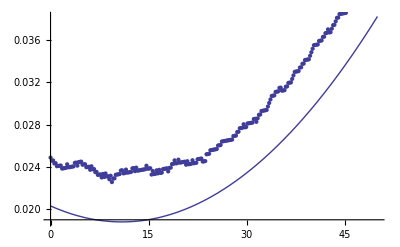

```mathematica
Show[Plot[nllm[x],{x,0,50}],ListPlot[Take[dat,{1,256}]⟦All,{1,3}⟧]]
```

```mathematica
Head[nllm[2]]
```

FittedModel